```mathematica
(*This work is licensed under the Creative Commons 4.0 License.
To view a copy of the license,visit http://creativecommons.org/licenses/by/4.0/
-Graphics-
Benjamin Schäfer, benjamin.schaefer@ds.mpg.de
Network Dynamics, Max Planck Institute for Dynamics and Self-Organization*)
```

```mathematica
(*Build the characteristic equation as you did*)
Clear[τ,funOmega,funTheta,Θ,Ω,θ];
α=0.1; 
coupling=8; 
power={1,-1};
γ=0.25;
numberOfNodes=2;
adjacency=AdjacencyMatrix[StarGraph[numberOfNodes]];
(*Build Jacobian*)
funOmega[θ_,ω_,i_List]:=power[[i]]-α*ω[[i]]+Sum[adjacency[[i,j]]*coupling*Sin[θ[[j]]-θ[[i]]],{j,1,numberOfNodes}];
funTheta[θ_,ω_,i_List]:=ω[[i]];
Θ=Array[θ,numberOfNodes]; (*http://reference.wolfram.com/language/tutorial/MakingDefinitionsForIndexedObjects.html*)
Ω=Array[ω,numberOfNodes];
a=D[funTheta[Θ,Ω,i]/.i->Table[j,{j,numberOfNodes}],{Θ}];
b=D[funTheta[Θ,Ω,i]/.i->Table[j,{j,numberOfNodes}],{Ω}];
c=D[funOmega[Θ,Ω,i]/.i->Table[j,{j,numberOfNodes}],{Θ}];
d=D[funOmega[Θ,Ω,i]/.i->Table[j,{j,numberOfNodes}],{Ω}];
jac=ArrayFlatten[{{a,b},{c,d}}];
jacD=ArrayFlatten[{{ConstantArray[0,{numberOfNodes,numberOfNodes}],0},{0,-IdentityMatrix[2]*Exp[-λ*τ]*γ}}];
charEqMatrix=jac+jacD-λ*IdentityMatrix[2*numberOfNodes];
(*Define fixed point*)
invars=Table[x[i],{i,1,numberOfNodes}];
inconds=Table[{x[i],0},{i,1,numberOfNodes}];
ineqns=Table[power[[i]]==-Sum[adjacency[[i,j]]*coupling*Sin[x[j]-x[i]],{j,1,numberOfNodes}],{i,1,numberOfNodes}];
invals=Table[x[i]/.FindRoot[ineqns,inconds],{i,1,numberOfNodes}];
Do[θ[i]=invals[[i]],{i,1,numberOfNodes}];
eqn={Det[charEqMatrix]/λ} ;(*divide by λ. No idea why the equation is not reduced then...*)
(*Apply Simplify to get the reduced equation, AND: do not set ==0, otherwise we loose a factor Exp[λτ]*)
Simplify@eqn
```

{ⅇ^(-2 λ τ) (0.0625 λ+ⅇ^(λ τ) (3.96863+0.05 λ+0.5 λ^2)+ⅇ^(2 λ τ) (1.58745+15.8845 λ+0.2 λ^2+1. λ^3))}

## (*Find the roots by sampling a pre-defined band *)

Some comments regarding timing: On my Laptop this takes ~80 sec with 4 i7 cores running, when using maxDelay=10;stepSizeDelay=0.05;

```mathematica
(*Lets assume we have the characteristic equation, you could re-write the above to return the characteristic function as a function and divide it by λ*)
Clear[eqn];
eqn[λ_,τ_]:=(*1/λ**)ⅇ^(-2 λ τ) λ (0.0625 λ+ⅇ^(λ τ) (3.968626966596886+0.05 λ+0.5 λ^2)+ⅇ^(2 λ τ) (1.5874507866387546+15.884507866387544 λ+0.2 λ^2+1. λ^3));
(*Turn off some unneccessary messages (be careful to know what you do)*)
Off[InterpolatingFunction::dmval];ParallelEvaluate[Off[InterpolatingFunction::dmval];Off[FindRoot::lstol]];
Off[FrontEndObject::notavail];ParallelEvaluate[Off[FrontEndObject::notavail]];Off[FindRoot::precw];
(*Set the sampling delay*)
minDelay=0;
stepSizeDelay=0.05;
maxDelay=10;
(*How deep and how mich do we want to sample?*)
cutOff=-100;
numberOfTrysForMinimalDelay=1000;
(*Generate a list of eigenvalues for delay τ=stepSizeDelay*)
λsamplingDelayUnfiltered=Table[λ/.FindRoot[eqn[λ,stepSizeDelay+minDelay]== 0,{λ,RandomComplex[{cutOff-15I,10+15I}]+0.01I},MaxIterations->10000,WorkingPrecision->30,AccuracyGoal->4],{numberOfTrysForMinimalDelay}];
λsamplingDelayFiltered=DeleteDuplicates[λsamplingDelayUnfiltered,Abs[#1-#2]<10^-4&];
numberOfEigenvalues=Length[λsamplingDelayFiltered];
(*define table for all eigenvalues and all delays*)
λTowardsMaxDelay=Table[0,{i,1,numberOfEigenvalues},{τcounter,1,(maxDelay-stepSizeDelay-minDelay)/stepSizeDelay+1}];
λTowardsMaxDelay[[All,1]]=λsamplingDelayFiltered;
(*Based on the initial eigenvalues found at τ=stepSizeDelay, assume that the curves are smooth and continue along the so far determined eigenvalues*)

(*Explicitly determine the eigenvalues for τcounter=2 and 3*)
Do[
τ=stepSizeDelay+(τcounter-1)*stepSizeDelay;
λTowardsMaxDelay[[index,τcounter]]=λ/.FindRoot[eqn[λ,τ]== 0,{λ,λTowardsMaxDelay[[index,τcounter-1]]+0.01*I},PrecisionGoal->4,AccuracyGoal->4, MaxIterations->300][[1]];
,{index,numberOfEigenvalues},{τcounter,2,3}];
(*Continue for τcounter≥3, to use extrapolation to find next eigenvalue*)
DistributeDefinitions[eqn];
SetSharedVariable[τcounter,stepSizeDelay,λTowardsMaxDelay,λTowardsZero];
Do[
λTowardsMaxDelay[[All,τcounter]]=ParallelTable[
(*calculate the actual delay for the iteration*)
τ=minDelay+stepSizeDelay+(τcounter-1)*stepSizeDelay;
(*the new eigenvalue is found by using the previous one; the iteration starts delayed by three as they were calculated already;
note that we add a small imaginary number to the previous λ to allow real eigenvalues to become complex*)
initialGuess=Interpolation[{{(τcounter-3-1)*stepSizeDelay,Indexed[λTowardsMaxDelay,{index,τcounter-3}]},{(τcounter-2-1)*stepSizeDelay,Indexed[λTowardsMaxDelay,{index,τcounter-2}]},{(τcounter-1-1)*stepSizeDelay,Indexed[λTowardsMaxDelay,{index,τcounter-1}]}},InterpolationOrder->2][(τcounter-1)*stepSizeDelay];
λ/.FindRoot[eqn[λ,τ]== 0,{λ,initialGuess+0.01*I},PrecisionGoal->4,AccuracyGoal->4, MaxIterations->300][[1]]
,{index,numberOfEigenvalues}],{τcounter,4,(maxDelay-stepSizeDelay-minDelay)/stepSizeDelay+1}];
```

```mathematica
(*Export longer calculation*)
SetDirectory[NotebookDirectory[]];
Export["2 node eigenvalues 0.05 to 10.wdx",λTowardsMaxDelay];
```

```mathematica
(*Import longer calculation*)
SetDirectory[NotebookDirectory[]];
λTowardsMaxDelay=Import["2 node eigenvalues 0.05 to 10.wdx"];
```

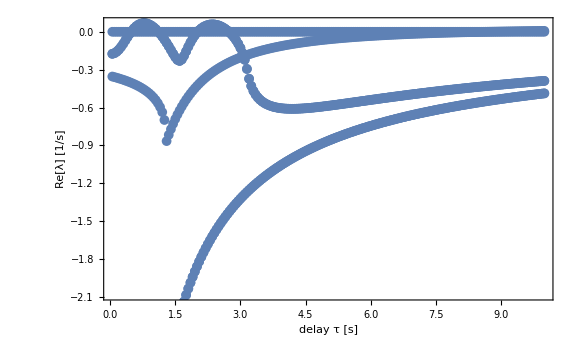

```mathematica
(*Show the results in a ListPlot: The highest curve  is the mode we typically see when considering only the difference. The initially middle curve then destabilizes the system for large delays; we are missing many other curves, that all start at very negative real parts and would contribute to the oscillations. You can find those if you 
a) start the extensive random sampling at a higher delay
b) when you increase the parameter "offset" to VERY negative numbers ~-10^3...-10^10*)
maxDelay=10;
stepSizeDelay=0.05;

markersize=10;
colorValue=0.1;
DiscretePlot[
Flatten[Re[Transpose[λTowardsMaxDelay][[Round[τ/(stepSizeDelay),1]]]]],
(*take real part of the root, put all different starting values together for one given delay τ*)
{τ,stepSizeDelay,maxDelay,stepSizeDelay},
PlotMarkers->{Automatic,markersize}, (*uses Dots(automatic), medium sized*)
LabelStyle->Directive[12,FontFamily->"Arial"], (*enlarges axes-labels*)
Frame->True,
FrameLabel-> {"delay τ [s]","Re[λ] [1/s]"}, 
Filling->None, (*prevents l;ines from x-axes to points*)
(*Joined->True,(*connects points*)*)
(*PlotStyle->Directive[Thick,ColorData["BlueGreenYellow",colorValue]],*)
PlotRangeClipping->True,
ImageSize->Large
]
```